## Process Experiment 32 Scattering Data

## Initialization code

### Check for CurveFit

```mathematica
Needs["CurveFit`"];
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

### Select an XY range to keep or remove

```mathematica
Clear[SetXYRange];
SetXYRange[plot:Blank[Graphics],OptionsPattern[{Log->{False,False},Label->""}]]:=Quiet[Block[{xr,yr,xinit1,yinit1,xinit2,yinit2,value,title,windowopts},If[!Check[{xr,yr}=PlotRange/.AbsoluteOptions[plot,PlotRange],False],Message[SetXRange::plotrange];Return[$Canceled]];If[xr=={0.,1.},xr={Min[xx],Max[xx]}];If[yr=={0.,1.},yr={Min[yy],Max[yy]}];xinit1=(Plus@@xr+xr[[1]])/3.;yinit1=(Plus@@yr+yr[[1]])/3.;xinit2=(Plus@@xr+xr[[2]])/3.;yinit2=(Plus@@yr+yr[[2]])/3.;title="Set X and Y Ranges";windowopts=If[$VersionNumber==6.&&$ReleaseNumber==0,{WindowTitle->title,WindowFloating->True},{WindowTitle->title,WindowSize->{Scaled[0.35],All},WindowFloating->True}];DynamicModule[{pt={{xinit1,yinit1},{xinit2,yinit2}},log=OptionValue[Log],prompt=OptionValue[Label],x1,x2,y1,y2},
If[Head[log]=!=List||Length[log]≠2,Clear[log]; log={False,False}];If[log[[1]]=!=True,log[[1]]=False];If[log[[2]]=!=True,log[[2]]=False];If[!StringQ[prompt],prompt=""];value=If[ChoiceDialog[Column[{prompt,Style["Drag the red lines to set the X and Y values:",Larger,Bold],Item[LocatorPane[Dynamic[pt],Show[plot,AspectRatio->1.0,Background->White,ImageSize->Scaled[1.]],Appearance->Graphics[{Red,Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]},ImageSize->Scaled[2]]],Frame->True],Grid[{{Style["X1 = ",Larger,Bold],Style[Dynamic[x1=Min[If[log[[1]],Exp[pt[[1,1]]],pt[[1,1]]],If[log[[1]],Exp[pt[[2,1]]],pt[[2,1]]]]],Larger,Bold],
Style["   Y1 = ",Larger,Bold],Style[Dynamic[y1=Min[If[log[[2]],Exp[pt[[1,2]]],pt[[1,2]]],If[log[[2]],Exp[pt[[2,2]]],pt[[2,2]]]]],Larger,Bold]},{Style["X2 = ",Larger,Bold],Style[Dynamic[x2=Max[If[log[[1]],Exp[pt[[1,1]]],pt[[1,1]]],If[log[[1]],Exp[pt[[2,1]]],pt[[2,1]]]]],Larger,Bold],
Style["   Y2 = ",Larger,Bold],Style[Dynamic[y2=Max[If[log[[2]],Exp[pt[[1,2]]],pt[[1,2]]],If[log[[2]],Exp[pt[[2,2]]],pt[[2,2]]]]],Larger,Bold]}}]},Spacings->1.5],Sequence@@windowopts],{{x1,x2},{y1,y2}},$Canceled]];value],{Ticks::ticks}]
```

```mathematica
Clear[KeepXY];
KeepXY[]:=Block[{range=SetXYRange[ScatterDataPlot[]],xmin,xmax,ymin,ymax,data={},num,i},
If[range===$Canceled,Return[$Canceled]];
SaveForUndo[];
{{xmin,xmax},{ymin,ymax}}=range;
For[i=1,i≤n,++i,
If[(xmin≤xx[[i]]≤xmax)&&(ymin≤yy[[i]]≤ymax),
AppendTo[data,{xx[[i]],yy[[i]]}]
]
];
num=Length[data];
sx=sy=ConstantArray[0,num];
{xx,yy}=Transpose[data];
n=num;
Print["n = "<>ToString[n]];
Print["Undo[] to return to previous data set."];
ScatterDataPlot[AspectRatio->1]
]
KeepXY::usage="KeepXY [ ] opens a dialog box to select a subset of the "<>
"current data set. Dragging the red lines on the plot identifies a "<>
"rectangular block of the data set to keep. Returns a "<>
"ScatterPlot[ ] of the new data set. Use Undo[ ] to recover "<>
"the original data set.";
```

```mathematica
Clear[RemoveXY];
RemoveXY[]:=Block[{range=SetXYRange[ScatterDataPlot[]],xmin,xmax,ymin,ymax,data={},num,i},
If[range===$Canceled,Return[$Canceled]];
SaveForUndo[];
{{xmin,xmax},{ymin,ymax}}=range;
For[i=1,i≤n,++i,
If[!((xmin≤xx[[i]]≤xmax)&&(ymin≤yy[[i]]≤ymax)),
AppendTo[data,{xx[[i]],yy[[i]]}]
]
];
num=Length[data];
sx=sy=ConstantArray[0,num];
{xx,yy}=Transpose[data];
n=num;
Print["n = "<>ToString[n]];
Print["Undo[] to return to previous data set."];
ScatterDataPlot[AspectRatio->1]
]
RemoveXY::usage="RemoveXY [ ] opens a dialog box to select a subset of the "<>
"current data set. Dragging the red lines on the plot identifies a "<>
"rectangular block of the data set to remove. Returns a "<>
"ScatterPlot[ ] of the new data set. Use Undo[ ] to recover "<>
"the original data set.";
```

### Scatter Plot to detector spectrum functions

```mathematica
Clear[xy2x];
xy2x[]:=Block[{xdata,ydata,num,xsig,ysig,data},
num=Floor[Max[xx]]+1;
xdata=Range[0,num-1];
ydata=ConstantArray[0,num];
Scan[(++ydata[[Floor[#]+1]])&,xx];
data=Select[Transpose[{xdata,ydata}],#[[2]]>0&];
{xdata,ydata}=Transpose[data];
num=Length[xdata];
SaveForUndo[];
sx=sy=ConstantArray[0,num];
{n,xx,yy}={num,xdata,1.0 ydata};
Print["n = "<>ToString[n]];
MakePoisson[Xerrors -> False];
Print["Undo[] once to get rid of channel count sigmas."];
Print["Undo[] again to return to Scatter Data."];
Block[{CurveFit`$DataSizeThreshold={0,0}},LinearDataPlot[] ]
]
xy2x::usage="xy2x [ ] converts a scatter plot to an X (target scintillator) "<>
"histogram and assigns Poisson count uncertainties. It generates a plot "<>
"of the resulting data set. Use Undo[ ] twice to return to the original "<>
"data set.";
```

```mathematica
Clear[xy2y];
xy2y[]:=Block[{xdata,ydata,num,xsig,ysig,data},
num=Floor[Max[yy]]+1;
xdata=Range[0,num-1];
ydata=ConstantArray[0,num];
Scan[(++ydata[[Floor[#]+1]])&,yy];
data=Select[Transpose[{xdata,ydata}],#[[2]]>0&];
{xdata,ydata}=Transpose[data];
num=Length[xdata];
SaveForUndo[];
sx=sy=ConstantArray[0,num];
{n,xx,yy}={num,xdata,1.0 ydata};
Print["n = "<>ToString[n]];
MakePoisson[Xerrors -> False];
Print["Undo[] once to get rid of channel count sigmas."];
Print["Undo[] again to return to Scatter Data."];
Block[{CurveFit`$DataSizeThreshold={0,0}},LinearDataPlot[] ]
]
xy2y::usage="xy2y [ ] converts a scatter plot to a Y (NaI scintillator) "<>
"histogram and assigns Poisson count uncertainties. It generates a plot "<>
"of the resulting data set. Use Undo[ ] twice to return to the original "<>
"data set.";
```

### Cleanup

```mathematica
SelectionMove[EvaluationNotebook[],After,Notebook]
```

## The defined functions’ usage messages

```mathematica
?KeepXY
?RemoveXY
?xy2x
?xy2y
```

KeepXY [ ] opens a dialog box to select a subset of the current data set. Dragging the red lines on the plot identifies a rectangular block of the data set to keep. Returns a ScatterPlot[ ] of the new data set. Use Undo[ ] to recover the original data set.

RemoveXY [ ] opens a dialog box to select a subset of the current data set. Dragging the red lines on the plot identifies a rectangular block of the data set to remove. Returns a ScatterPlot[ ] of the new data set. Use Undo[ ] to recover the original data set.

xy2x [ ] converts a scatter plot to an X (target scintillator) histogram and assigns Poisson count uncertainties. It generates a plot of the resulting data set. Use Undo[ ] twice to return to the original data set.

xy2y [ ] converts a scatter plot to a Y (NaI scintillator) histogram and assigns Poisson count uncertainties. It generates a plot of the resulting data set. Use Undo[ ] twice to return to the original data set.

## Working area

### 40 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_40.xy.mca

File comment header:

Spectrum #00004	3:03:43 PM 6/7/2018  Time: 626.36 ; XY Scatter Event Data
40 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 4298 data points.

n = 1362

Undo[] to return to previous data set.

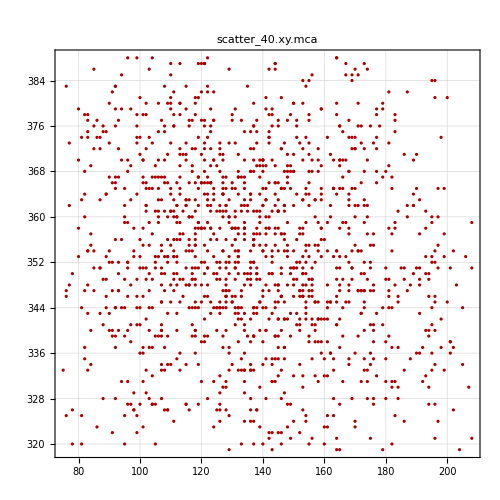

```mathematica
KeepXY[]
```

n = 133

Sorted data in order of increasing X values.

133 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

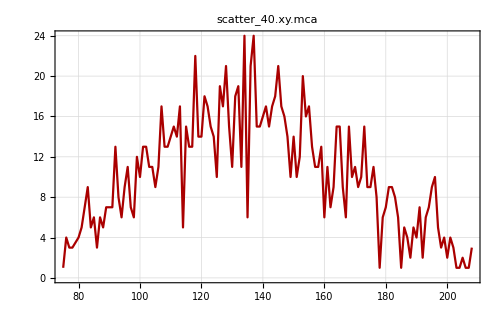

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 133

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
15.7997 | c= 
0.802434 | 
σ_y_max= 
2.19985 | σ_c= 
1.6158 | 
μ= 
134.288 | sigma= 
33.4861 | 
σ_μ= 
1.29103 | σ_sigma= 
5.09418 | Std. deviation= 
3.11307

Fit of (x,y±σ_y)

y_max= 
14.9556 | c= 
0.695793 | 
σ_y_max= 
0.774352 | σ_c= 
0.632289 | 
μ= 
132.636 | sigma= 
30.3599 | 
σ_μ= 
1.11627 | σ_sigma= 
2.31373 | χ^2/(n-4)= 
1.34211

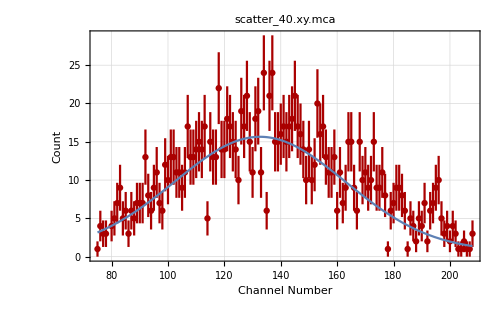
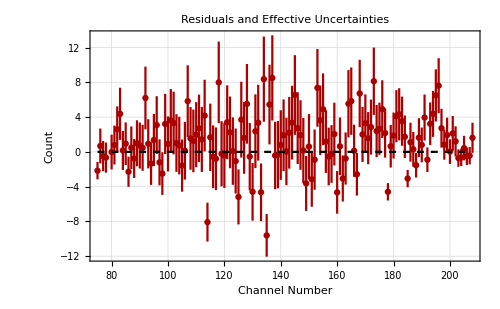
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
14.9556 | c= 
0.695793 | 
σ_y_max= 
0.774352 | σ_c= 
0.632289 | 
μ= 
132.636 | sigma= 
30.3599 | 
σ_μ= 
1.11627 | σ_sigma= 
2.31373 | χ^2/(n-4)= 
1.34211

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
xData={};
```

```mathematica
AppendTo[xData,{40,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_40.xy.mca

n = 1362

n = 70

Sorted data in order of increasing X values.

70 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

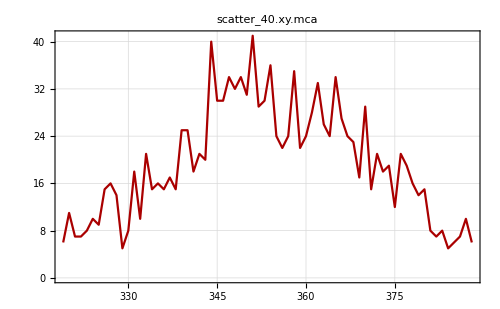

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 70

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
28.2107 | c= 
2.94049 | 
σ_y_max= 
4.07119 | σ_c= 
3.58358 | 
μ= 
354.123 | sigma= 
17.0228 | 
σ_μ= 
0.741904 | σ_sigma= 
2.71974 | Std. deviation= 
4.64457

Fit of (x,y±σ_y)

y_max= 
26.4203 | c= 
4.10615 | 
σ_y_max= 
2.08407 | σ_c= 
1.73134 | 
μ= 
354.386 | sigma= 
15.4963 | 
σ_μ= 
0.647671 | σ_sigma= 
1.81144 | χ^2/(n-4)= 
1.10695

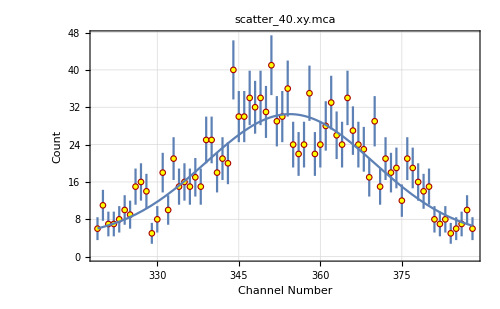
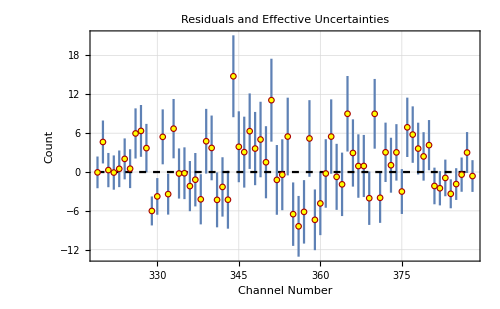
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
26.4203 | c= 
4.10615 | 
σ_y_max= 
2.08407 | σ_c= 
1.73134 | 
μ= 
354.386 | sigma= 
15.4963 | 
σ_μ= 
0.647671 | σ_sigma= 
1.81144 | χ^2/(n-4)= 
1.10695

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
yData={};
```

```mathematica
AppendTo[yData,{40,mean,sigmean}];
```

### 60 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_60.xy.mca

File comment header:

Spectrum #00006	3:30:22 PM 6/7/2018  Time: 553.36 ; XY Scatter Event Data
60 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2996 data points.

n = 1003

Undo[] to return to previous data set.

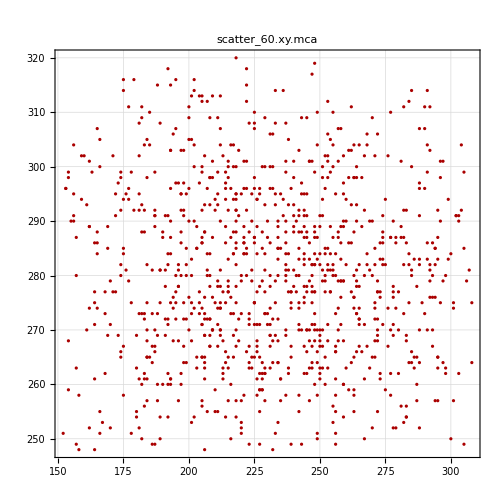

```mathematica
KeepXY[]
```

n = 157

Sorted data in order of increasing X values.

157 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

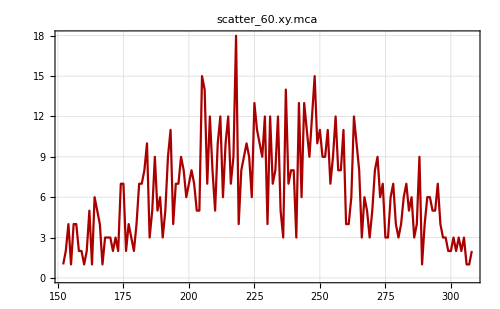

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{ 67,68,79,90}
```

n= 156

1 point removed.

n= 155

1 point removed.

n= 154

1 point removed.

n= 153

1 point removed.

{Null,Null,Null,Null}

```mathematica
GaussianCFit[]
```

n = 153

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
10.803 | c= 
-1.33814 | 
σ_y_max= 
8.28419 | σ_c= 
8.51633 | 
μ= 
231.143 | sigma= 
50.559 | 
σ_μ= 
1.93265 | σ_sigma= 
25.671 | Std. deviation= 
2.47254

Fit of (x,y±σ_y)

y_max= 
9.29206 | c= 
-1.14376 | 
σ_y_max= 
3.66407 | σ_c= 
3.90427 | 
μ= 
231.659 | sigma= 
48.527 | 
σ_μ= 
1.69465 | σ_sigma= 
15.8216 | χ^2/(n-4)= 
1.05839

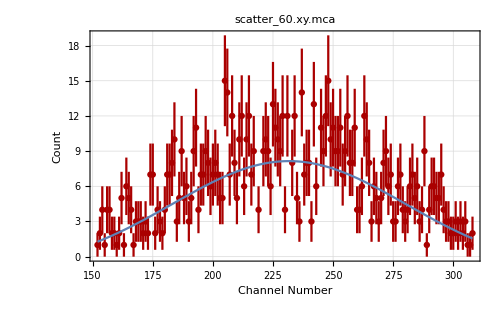
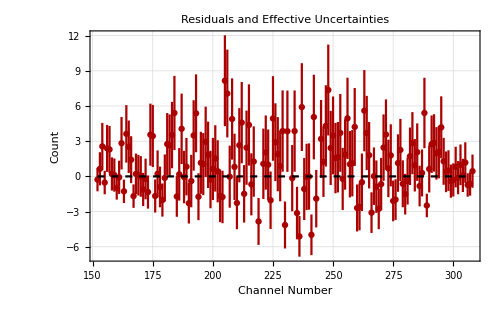
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
9.29206 | c= 
-1.14376 | 
σ_y_max= 
3.66407 | σ_c= 
3.90427 | 
μ= 
231.659 | sigma= 
48.527 | 
σ_μ= 
1.69465 | σ_sigma= 
15.8216 | χ^2/(n-4)= 
1.05839

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{60,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_60.xy.mca

n = 1003

n = 73

Sorted data in order of increasing X values.

73 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

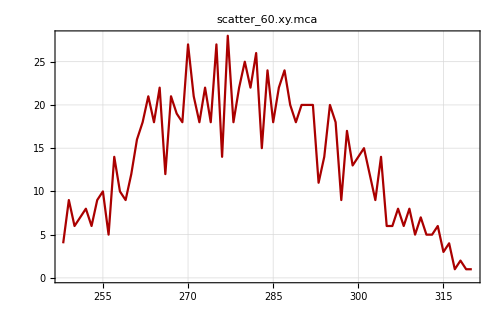

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 73

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
24.9823 | c= 
-2.58455 | 
σ_y_max= 
4.57494 | σ_c= 
4.87688 | 
μ= 
279.377 | sigma= 
20.8536 | 
σ_μ= 
0.68154 | σ_sigma= 
3.50933 | Std. deviation= 
3.15897

Fit of (x,y±σ_y)

y_max= 
24.2247 | c= 
-2.69883 | 
σ_y_max= 
2.41656 | σ_c= 
2.82003 | 
μ= 
279.698 | sigma= 
20.6341 | 
σ_μ= 
0.692554 | σ_sigma= 
2.62177 | χ^2/(n-4)= 
0.745444

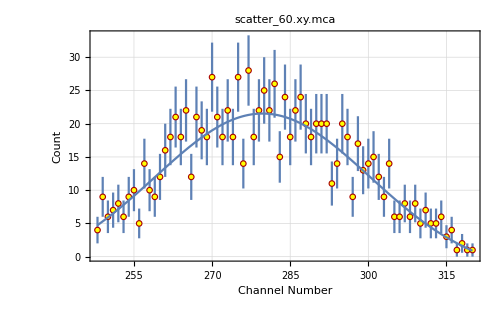
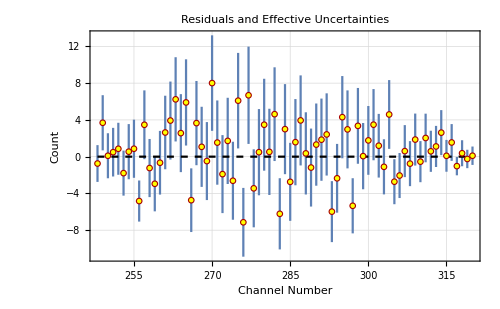
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
24.2247 | c= 
-2.69883 | 
σ_y_max= 
2.41656 | σ_c= 
2.82003 | 
μ= 
279.698 | sigma= 
20.6341 | 
σ_μ= 
0.692554 | σ_sigma= 
2.62177 | χ^2/(n-4)= 
0.745444

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{60,mean,sigmean}];
```

### 80 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_80.xy.mca

File comment header:

Spectrum #00008	4:06:47 PM 6/7/2018  Time: 1454.27 ; XY Scatter Event Data
80 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 6086 data points.

n = 2129

Undo[] to return to previous data set.

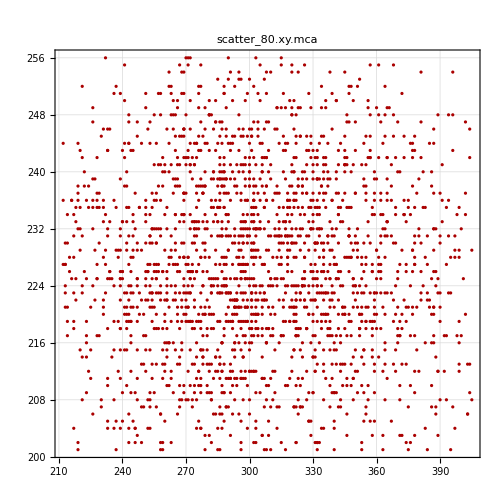

```mathematica
KeepXY[]
```

n = 194

Sorted data in order of increasing X values.

194 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

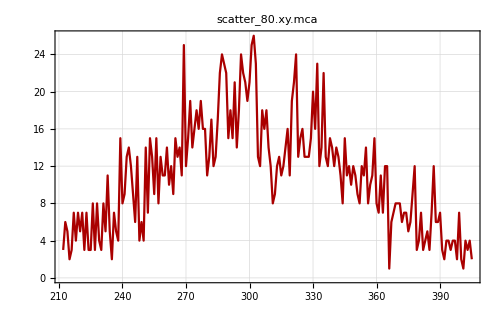

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 194

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
16.1134 | c= 
1.60426 | 
σ_y_max= 
1.85277 | σ_c= 
1.43838 | 
μ= 
302.021 | sigma= 
46.9047 | 
σ_μ= 
1.60672 | σ_sigma= 
6.10737 | Std. deviation= 
3.4042

Fit of (x,y±σ_y)

y_max= 
15.207 | c= 
1.69228 | 
σ_y_max= 
0.761096 | σ_c= 
0.663175 | 
μ= 
302.345 | sigma= 
42.1452 | 
σ_μ= 
1.36054 | σ_sigma= 
3.19759 | χ^2/(n-4)= 
1.21439

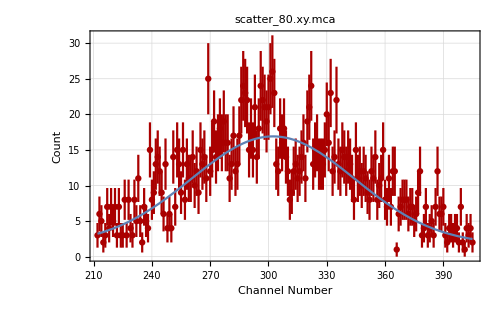
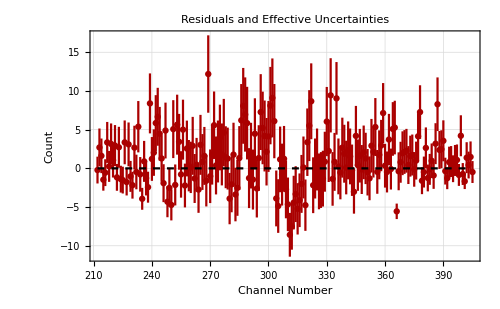
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
15.207 | c= 
1.69228 | 
σ_y_max= 
0.761096 | σ_c= 
0.663175 | 
μ= 
302.345 | sigma= 
42.1452 | 
σ_μ= 
1.36054 | σ_sigma= 
3.19759 | χ^2/(n-4)= 
1.21439

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{80,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_80.xy.mca

n = 2129

n = 56

Sorted data in order of increasing X values.

56 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

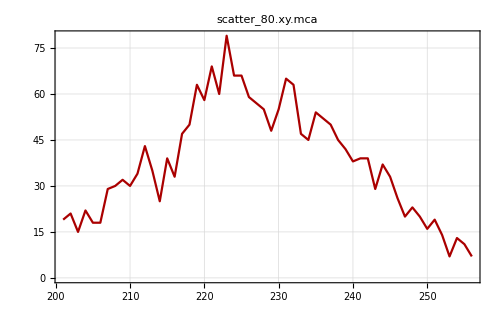

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 56

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
56.2881 | c= 
5.68518 | 
σ_y_max= 
6.10719 | σ_c= 
4.8607 | 
μ= 
226.634 | sigma= 
13.3327 | 
σ_μ= 
0.44207 | σ_sigma= 
1.69203 | Std. deviation= 
6.28071

Fit of (x,y±σ_y)

y_max= 
58.7817 | c= 
1.17445 | 
σ_y_max= 
4.93753 | σ_c= 
4.13823 | 
μ= 
226.749 | sigma= 
14.4076 | 
σ_μ= 
0.387345 | σ_sigma= 
1.56972 | χ^2/(n-4)= 
1.04349

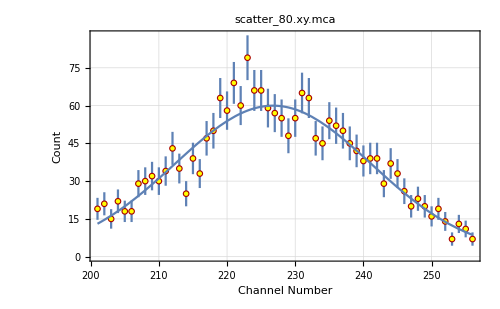
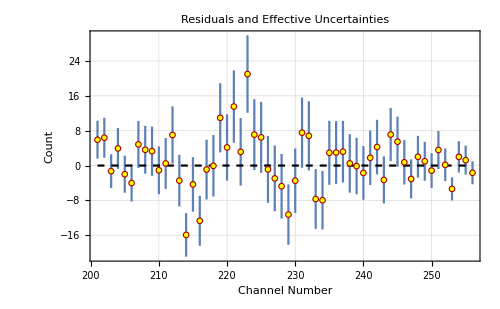
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
58.7817 | c= 
1.17445 | 
σ_y_max= 
4.93753 | σ_c= 
4.13823 | 
μ= 
226.749 | sigma= 
14.4076 | 
σ_μ= 
0.387345 | σ_sigma= 
1.56972 | χ^2/(n-4)= 
1.04349

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{80,mean,sigmean}];
```

### 100 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_100.xy.mca

File comment header:

Spectrum #00009	4:16:26 PM 6/7/2018  Time: 528.96 ; XY Scatter Event Data
100 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2012 data points.

n = 704

Undo[] to return to previous data set.

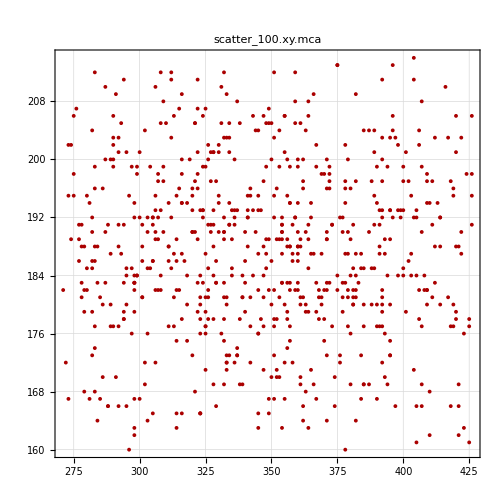

```mathematica
KeepXY[]
```

n = 154

Sorted data in order of increasing X values.

154 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

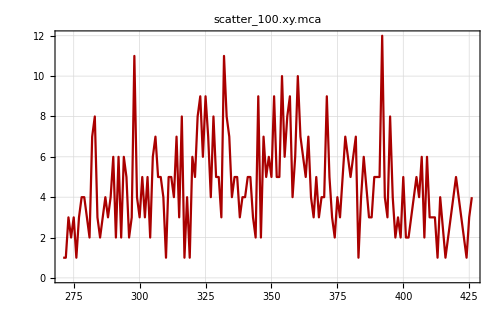

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{28}
```

n= 152

1 point removed.

{Null}

```mathematica
GaussianCFit[]
```

n = 152

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
3.81682 | c= 
2.00889 | 
σ_y_max= 
4.49785 | σ_c= 
1.07168 | 
μ= 
345.316 | sigma= 
43.1507 | 
σ_μ= 
3.81612 | σ_sigma= 
71.4142 | Std. deviation= 
1.93879

Fit of (x,y±σ_y)

y_max= 
3.08151 | c= 
1.60418 | 
σ_y_max= 
2.43344 | σ_c= 
0.876048 | 
μ= 
349.291 | sigma= 
40.6876 | 
σ_μ= 
4.44023 | σ_sigma= 
3649.19 | χ^2/(n-4)= 
0.988598

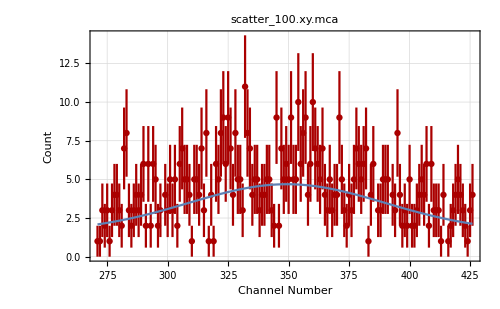
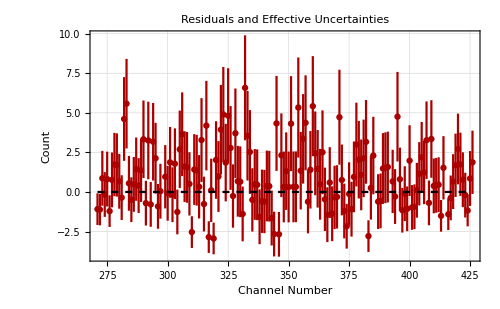
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
3.08151 | c= 
1.60418 | 
σ_y_max= 
2.43344 | σ_c= 
0.876048 | 
μ= 
349.291 | sigma= 
40.6876 | 
σ_μ= 
4.44023 | σ_sigma= 
3649.19 | χ^2/(n-4)= 
0.988598

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{100,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_100.xy.mca

n = 704

n = 55

Sorted data in order of increasing X values.

55 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

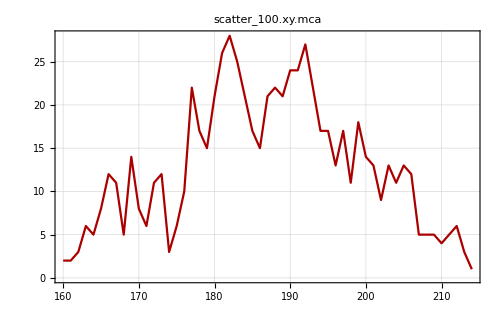

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 55

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
19.8858 | c= 
2.61267 | 
σ_y_max= 
2.79576 | σ_c= 
2.04741 | 
μ= 
187.536 | sigma= 
11.4252 | 
σ_μ= 
0.690038 | σ_sigma= 
2.27368 | Std. deviation= 
3.79403

Fit of (x,y±σ_y)

y_max= 
19.7508 | c= 
1.8952 | 
σ_y_max= 
1.28756 | σ_c= 
0.92032 | 
μ= 
188.513 | sigma= 
10.7196 | 
σ_μ= 
0.574773 | σ_sigma= 
1.24045 | χ^2/(n-4)= 
1.46893

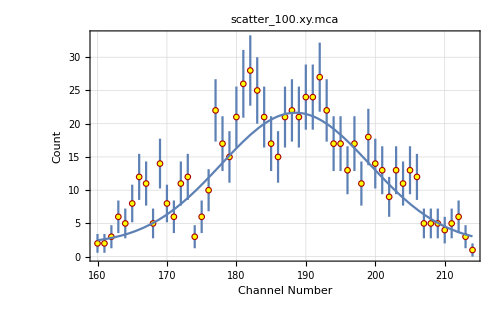
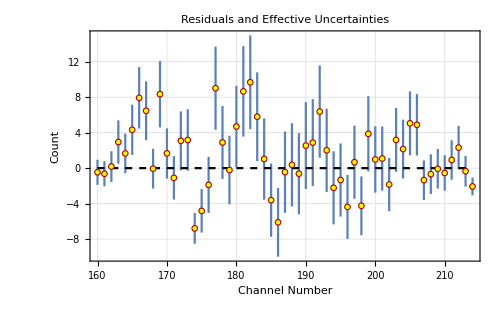
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
19.7508 | c= 
1.8952 | 
σ_y_max= 
1.28756 | σ_c= 
0.92032 | 
μ= 
188.513 | sigma= 
10.7196 | 
σ_μ= 
0.574773 | σ_sigma= 
1.24045 | χ^2/(n-4)= 
1.46893

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{100,mean,sigmean}];
```

### 120 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_120.xy.mca

File comment header:

Spectrum #00007	3:40:55 PM 6/7/2018  Time: 567.75 ; XY Scatter Event Data
120 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2175 data points.

n = 1038

Undo[] to return to previous data set.

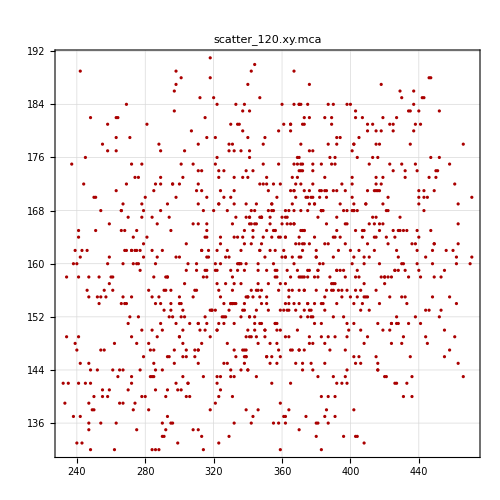

```mathematica
KeepXY[]
```

n = 230

Sorted data in order of increasing X values.

230 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

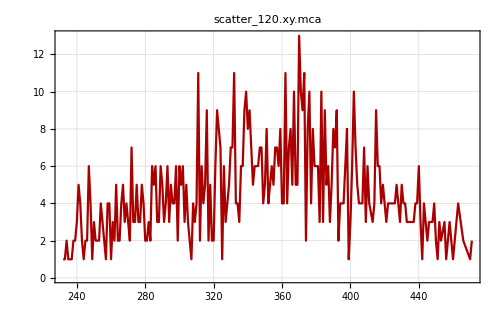

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 230

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
4.65221 | c= 
2.00546 | 
σ_y_max= 
0.827404 | σ_c= 
0.558659 | 
μ= 
359.561 | sigma= 
51.1911 | 
σ_μ= 
3.38108 | σ_sigma= 
11.8937 | Std. deviation= 
1.92458

Fit of (x,y±σ_y)

Calculating sigm

y_max= 
3.99783 | c= 
1.30416 | 
σ_y_max= 
1.27369 | σ_c= 
0.584287 | 
μ= 
360.741 | sigma= 
56.8461 | 
σ_μ= 
4.24652 | σ_sigma= 
22.1567 | χ^2/(n-4)= 
0.880585

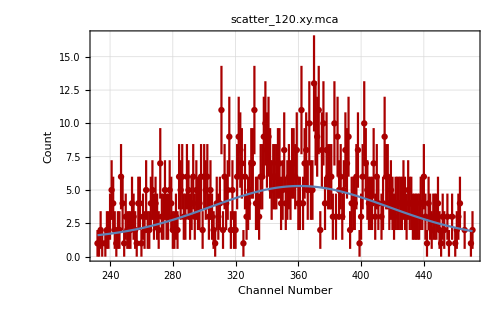
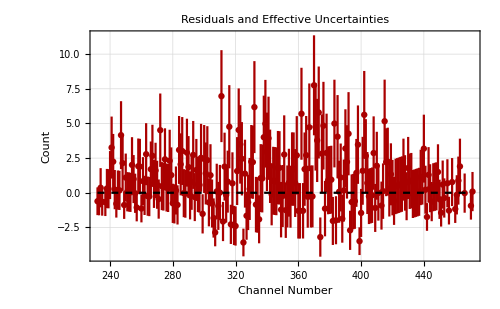
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
3.99783 | c= 
1.30416 | 
σ_y_max= 
1.27369 | σ_c= 
0.584287 | 
μ= 
360.741 | sigma= 
56.8461 | 
σ_μ= 
4.24652 | σ_sigma= 
22.1567 | χ^2/(n-4)= 
0.880585

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{120,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_120.xy.mca

n = 1038

n = 60

Sorted data in order of increasing X values.

60 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

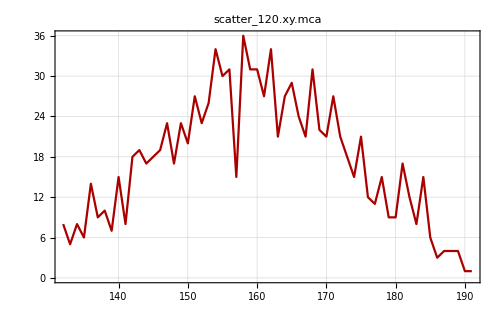

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 60

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
29.8781 | c= 
-0.972133 | 
σ_y_max= 
5.42878 | σ_c= 
5.90122 | 
μ= 
159.402 | sigma= 
15.4888 | 
σ_μ= 
0.571933 | σ_sigma= 
2.86305 | Std. deviation= 
3.94907

Fit of (x,y±σ_y)

y_max= 
32.1203 | c= 
-4.69935 | 
σ_y_max= 
3.6568 | σ_c= 
4.22351 | 
μ= 
159.316 | sigma= 
17.1331 | 
σ_μ= 
0.496917 | σ_sigma= 
2.34467 | χ^2/(n-4)= 
0.96631

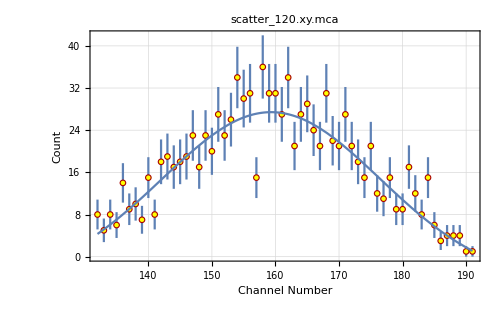
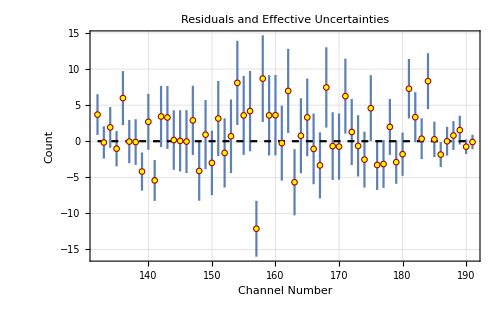
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
32.1203 | c= 
-4.69935 | 
σ_y_max= 
3.6568 | σ_c= 
4.22351 | 
μ= 
159.316 | sigma= 
17.1331 | 
σ_μ= 
0.496917 | σ_sigma= 
2.34467 | χ^2/(n-4)= 
0.96631

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{120,mean,sigmean}];
```

### 130 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_130.xy.mca

File comment header:

Spectrum #00011	4:36:41 PM 6/7/2018  Time: 486.44 ; XY Scatter Event Data
130 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 1943 data points.

n = 702

Undo[] to return to previous data set.

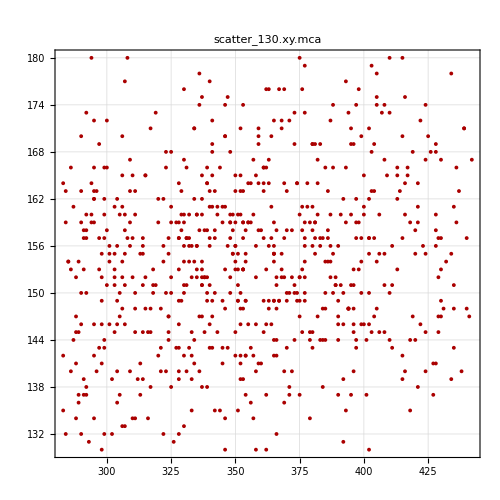

```mathematica
KeepXY[]
```

n = 158

Sorted data in order of increasing X values.

158 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

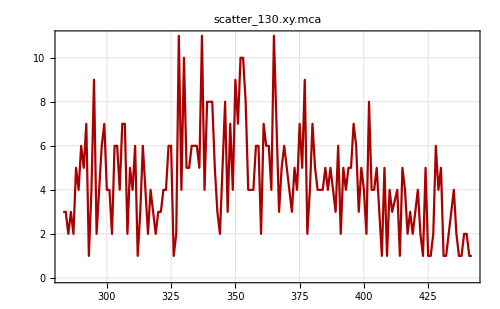

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{13,46}
```

n= 157

1 point removed.

n= 156

1 point removed.

{Null,Null}

```mathematica
GaussianCFit[]
```

n = 156

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
4.97327 | c= 
0.85772 | 
σ_y_max= 
10.5364 | σ_c= 
1.56921 | 
μ= 
349.626 | sigma= 
53.0201 | 
σ_μ= 
3.65075 | σ_sigma= 
79.205 | Std. deviation= 
1.98057

Fit of (x,y±σ_y)

y_max= 
4.26556 | c= 
0.496153 | 
σ_y_max= 
4.28188 | σ_c= 
1.06997 | 
μ= 
352.543 | sigma= 
49.8594 | 
σ_μ= 
3.65033 | σ_sigma= 
40.9078 | χ^2/(n-4)= 
0.982867

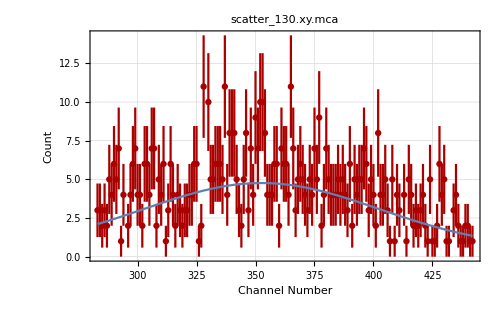
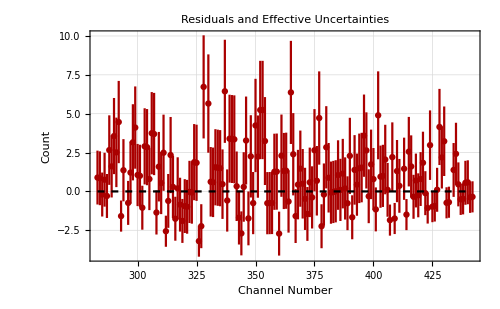
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
4.26556 | c= 
0.496153 | 
σ_y_max= 
4.28188 | σ_c= 
1.06997 | 
μ= 
352.543 | sigma= 
49.8594 | 
σ_μ= 
3.65033 | σ_sigma= 
40.9078 | χ^2/(n-4)= 
0.982867

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{130,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_130.xy.mca

n = 702

n = 51

Sorted data in order of increasing X values.

51 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

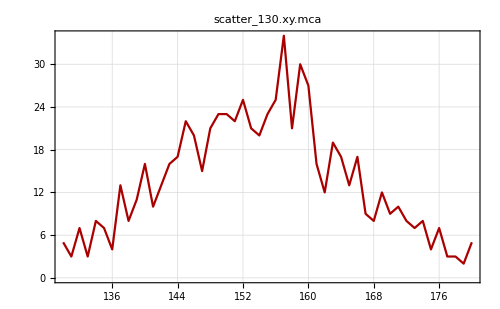

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 51

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
22.1546 | c= 
2.56721 | 
σ_y_max= 
2.06674 | σ_c= 
1.72782 | 
μ= 
153.98 | sigma= 
10.4402 | 
σ_μ= 
0.510594 | σ_sigma= 
1.39076 | Std. deviation= 
3.27685

Fit of (x,y±σ_y)

y_max= 
22.0973 | c= 
1.79622 | 
σ_y_max= 
1.56726 | σ_c= 
1.26034 | 
μ= 
153.896 | sigma= 
10.568 | 
σ_μ= 
0.532607 | σ_sigma= 
1.29822 | χ^2/(n-4)= 
0.736339

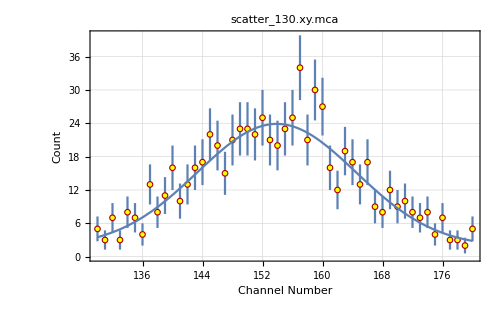
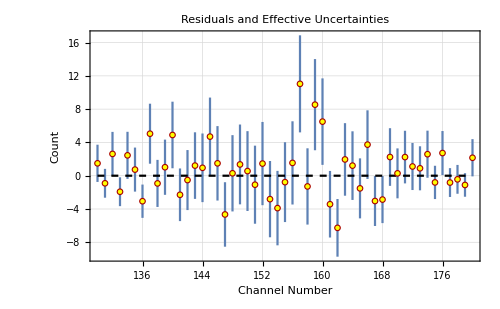
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
22.0973 | c= 
1.79622 | 
σ_y_max= 
1.56726 | σ_c= 
1.26034 | 
μ= 
153.896 | sigma= 
10.568 | 
σ_μ= 
0.532607 | σ_sigma= 
1.29822 | χ^2/(n-4)= 
0.736339

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{130,mean,sigmean}];
```

### 150 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_150.xy.mca

File comment header:

Spectrum #00005	3:20:09 PM 6/7/2018  Time: 854.28 ; XY Scatter Event Data
150 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 3311 data points.

n = 1704

Undo[] to return to previous data set.

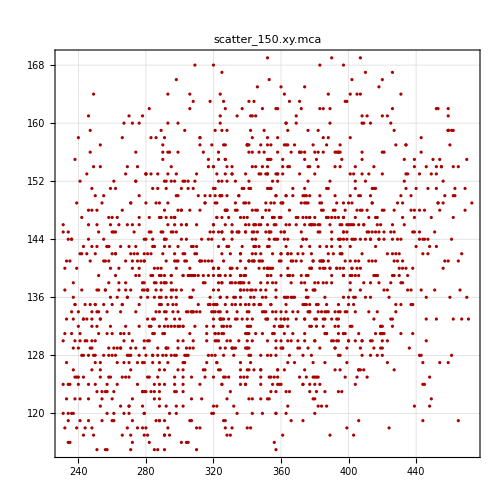

```mathematica
KeepXY[]
```

n = 237

Sorted data in order of increasing X values.

237 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

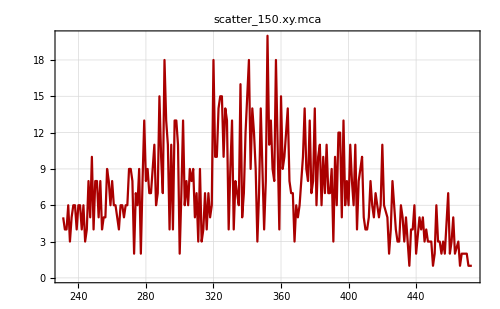

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{75,77}
```

n= 229

1 point removed.

n= 228

1 point removed.

{Null,Null}

```mathematica
GaussianCFit[]
```

n = 228

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
15.0513 | c= 
-5.14919 | 
σ_y_max= 
22.4486 | σ_c= 
35.2525 | 
μ= 
334.964 | sigma= 
107.802 | 
σ_μ= 
3.11039 | σ_sigma= 
111.394 | Std. deviation= 
2.8249

Fit of (x,y±σ_y)

y_max= 
14.07 | c= 
-5.7903 | 
σ_y_max= 
85.9889 | σ_c= 
72.9871 | 
μ= 
330.726 | sigma= 
120.379 | 
σ_μ= 
3.60567 | σ_sigma= 
274.349 | χ^2/(n-4)= 
1.08132

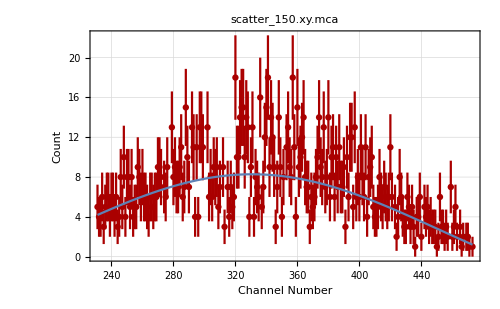
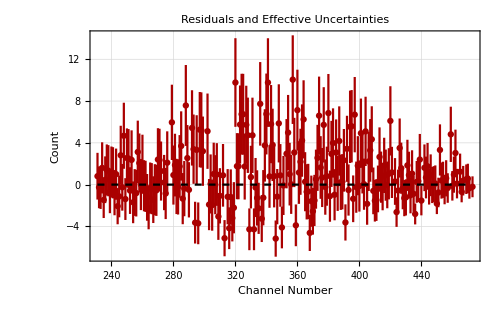
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
14.07 | c= 
-5.7903 | 
σ_y_max= 
85.9889 | σ_c= 
72.9871 | 
μ= 
330.726 | sigma= 
120.379 | 
σ_μ= 
3.60567 | σ_sigma= 
274.349 | χ^2/(n-4)= 
1.08132

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{150,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_150.xy.mca

n = 1704

n = 55

Sorted data in order of increasing X values.

55 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

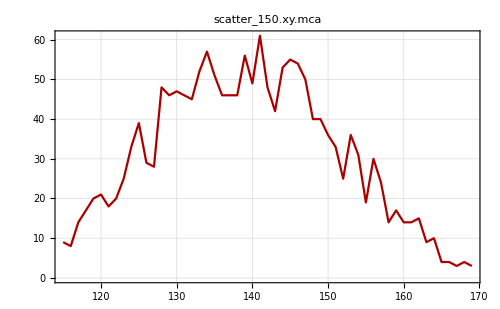

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 55

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
58.409 | c= 
-5.12061 | 
σ_y_max= 
5.37119 | σ_c= 
5.82291 | 
μ= 
138.821 | sigma= 
14.4829 | 
σ_μ= 
0.350487 | σ_sigma= 
1.38875 | Std. deviation= 
4.76571

Fit of (x,y±σ_y)

y_max= 
56.1225 | c= 
-3.08235 | 
σ_y_max= 
2.57393 | σ_c= 
2.9097 | 
μ= 
138.836 | sigma= 
13.7666 | 
σ_μ= 
0.357275 | σ_sigma= 
0.95142 | χ^2/(n-4)= 
0.716333

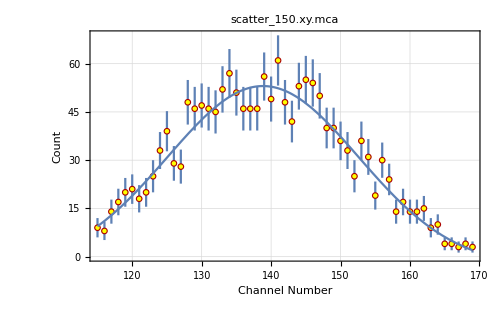
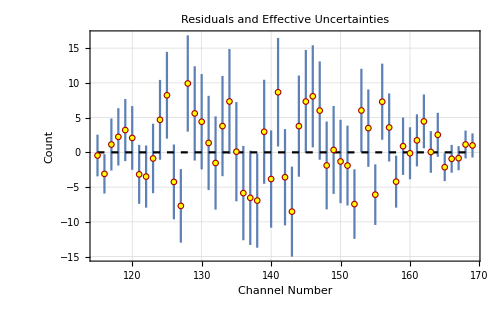
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
56.1225 | c= 
-3.08235 | 
σ_y_max= 
2.57393 | σ_c= 
2.9097 | 
μ= 
138.836 | sigma= 
13.7666 | 
σ_μ= 
0.357275 | σ_sigma= 
0.95142 | χ^2/(n-4)= 
0.716333

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_150.xy.mca

File comment header:

Spectrum #00005	3:20:09 PM 6/7/2018  Time: 854.28 ; XY Scatter Event Data
150 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 3311 data points.

n = 3311

Undo[] to return to previous data set.

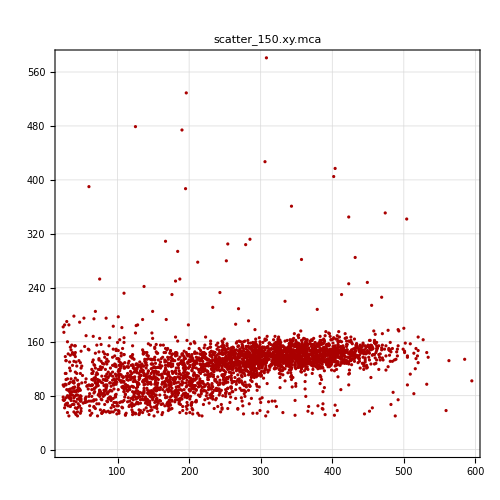

```mathematica
KeepXY[]
```

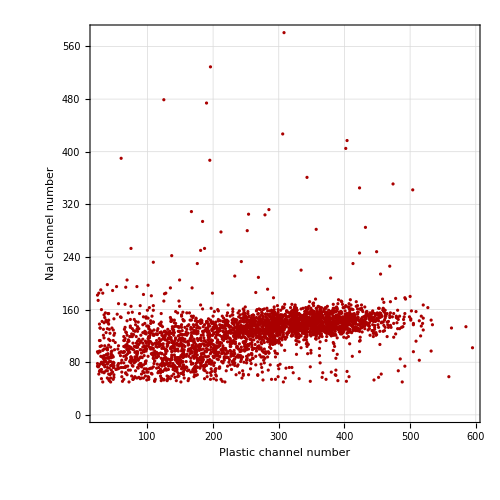

```mathematica
Show[%246,FrameLabel->{{HoldForm[NaI channel number],None},{HoldForm[Plastic channel number],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```